```mathematica
Plot3D[Cos[x]Cos[y/(√3)]-1/2 Cos[(2y)/(√3)],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
FourierTransform[Cos[x]Cos[y/(√3)]-1/2 Cos[(2y)/(√3)],{x,y},{kx,ky}]
```

3/2 π DiracDelta[-1+kx] DiracDelta[√3-3 ky]+3/2 π DiracDelta[1+kx] DiracDelta[√3-3 ky]-3/2 π DiracDelta[kx] DiracDelta[2 √3-3 ky]+3/2 π DiracDelta[-1+kx] DiracDelta[√3+3 ky]+3/2 π DiracDelta[1+kx] DiracDelta[√3+3 ky]-3/2 π DiracDelta[kx] DiracDelta[2 √3+3 ky]

```mathematica
3/2 π DiracDelta[-1+kx] DiracDelta[√3-3 ky]+3/2 π DiracDelta[1+kx] DiracDelta[√3-3 ky]-3/2 π DiracDelta[kx] DiracDelta[2 √3-3 ky]+3/2 π DiracDelta[-1+kx] DiracDelta[√3+3 ky]+3/2 π DiracDelta[1+kx] DiracDelta[√3+3 ky]-3/2 π DiracDelta[kx] DiracDelta[2 √3+3 ky]//TraditionalForm
```

3/2 π kx-1 √3-3 ky+3/2 π kx+1 √3-3 ky-3/2 π kx 2 √3-3 ky+3/2 π kx-1 3 ky+√3+3/2 π kx+1 3 ky+√3-3/2 π kx 3 ky+2 √3

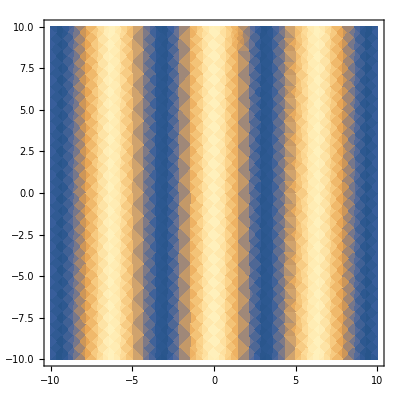

```mathematica
DensityPlot[Cos[x],{x,-10,10},{y,-10,10}]
FourierTransform[Cos[x],{x,y},{kx,ky}]
```

```mathematica
FourierTransform[Cos[x],{x,y},{kx,ky}]
```

π DiracDelta[-1+kx] DiracDelta[ky]+π DiracDelta[1+kx] DiracDelta[ky]

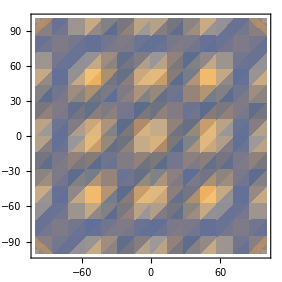

```mathematica
DensityPlot[(Cos[x]+Cos[x-y]+Cos[y]+Cos[x+y])/π,{x,-100,100},{y,-100,100}]
```

```mathematica
Plot3D[(Cos[x]+Cos[x-y]+Cos[y]+Cos[x+y])/π,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
FourierTransform[Cos[x]Sin[y],{x,y},{kx,ky}]
```

1/2 ⅈ π DiracDelta[-1+kx] DiracDelta[-1+ky]+1/2 ⅈ π DiracDelta[1+kx] DiracDelta[-1+ky]-1/2 ⅈ π DiracDelta[-1+kx] DiracDelta[1+ky]-1/2 ⅈ π DiracDelta[1+kx] DiracDelta[1+ky]

```mathematica
InverseFourierTransform[DiracDelta[kx]*DiracDelta[ky+1]+DiracDelta[kx]*DiracDelta[ky-1]+DiracDelta[kx+1]*DiracDelta[ky]+DiracDelta[kx-1]*DiracDelta[ky]+
DiracDelta[kx-1]*DiracDelta[ky+1]+DiracDelta[kx+1]*DiracDelta[ky+1]+DiracDelta[kx-1]*DiracDelta[ky-1]+DiracDelta[kx+1]*DiracDelta[ky-1],{kx,ky},{x,y}]
```

(ⅇ^(-ⅈ (x+y)) (1+ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)+ⅇ^(ⅈ y)+ⅇ^(2 ⅈ y)+ⅇ^(2 ⅈ (x+y))+ⅇ^(ⅈ (2 x+y))+ⅇ^(ⅈ (x+2 y))))/(2 π)

```mathematica
ExpToTrig[(ⅇ^(-ⅈ (x+y)) (1+ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)+ⅇ^(ⅈ y)+ⅇ^(2 ⅈ y)+ⅇ^(2 ⅈ (x+y))+ⅇ^(ⅈ (2 x+y))+ⅇ^(ⅈ (x+2 y))))/(2 π)]
```

1/(2 π)(Cos[x+y]-ⅈ Sin[x+y]) (1+Cos[x]+Cos[2 x]+Cos[y]+Cos[2 y]+Cos[2 (x+y)]+Cos[2 x+y]+Cos[x+2 y]+ⅈ Sin[x]+ⅈ Sin[2 x]+ⅈ Sin[y]+ⅈ Sin[2 y]+ⅈ Sin[2 (x+y)]+ⅈ Sin[2 x+y]+ⅈ Sin[x+2 y])

```mathematica
TrigReduce[1/(2 π)(Cos[x+y]-ⅈ Sin[x+y]) (1+Cos[x]+Cos[2 x]+Cos[y]+Cos[2 y]+Cos[2 (x+y)]+Cos[2 x+y]+Cos[x+2 y]+ⅈ Sin[x]+ⅈ Sin[2 x]+ⅈ Sin[y]+ⅈ Sin[2 y]+ⅈ Sin[2 (x+y)]+ⅈ Sin[2 x+y]+ⅈ Sin[x+2 y])]
```

(Cos[x]+Cos[x-y]+Cos[y]+Cos[x+y])/π

```mathematica
Plot3D[2Cos[(√3)/2 x]Cos[y/2]+Cos[y]+2Cos[(√3)/2 x]Cos[y/2+(2Pi)/3]+Cos[y+(4Pi)/3],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
2Cos[(√3)/2 x]Cos[y/2]+Cos[y]+2Cos[(√3)/2 x]Cos[y/2+(2Pi)/3]+Cos[y+(4Pi)/3]//Simplify
```

1/2 (Cos[y]+2 Cos[(√3 x)/2] (Cos[y/2]-√3 Sin[y/2])+√3 Sin[y])

```mathematica
FourierTransform[2Cos[(√3)/2 x]Cos[y/2]+Cos[y]+2Cos[(√3)/2 x]Cos[y/2+(2Pi)/3]+Cos[y+(4Pi)/3],{x,y},{kx,ky}]
```

2 π DiracDelta[√3-2 kx] DiracDelta[1-2 ky]-2 ⅈ √3 π DiracDelta[√3-2 kx] DiracDelta[1-2 ky]+2 π DiracDelta[√3+2 kx] DiracDelta[1-2 ky]-2 ⅈ √3 π DiracDelta[√3+2 kx] DiracDelta[1-2 ky]+1/2 π DiracDelta[kx] DiracDelta[-1+ky]+1/2 ⅈ √3 π DiracDelta[kx] DiracDelta[-1+ky]+1/2 π DiracDelta[kx] DiracDelta[1+ky]-1/2 ⅈ √3 π DiracDelta[kx] DiracDelta[1+ky]+2 π DiracDelta[√3-2 kx] DiracDelta[1+2 ky]+2 ⅈ √3 π DiracDelta[√3-2 kx] DiracDelta[1+2 ky]+2 π DiracDelta[√3+2 kx] DiracDelta[1+2 ky]+2 ⅈ √3 π DiracDelta[√3+2 kx] DiracDelta[1+2 ky]

```mathematica
k2=Table[i^2+j^2,{i,-10,10},{j,-10,10}]//Flatten//Sort//Union
```

{0,1,2,4,5,8,9,10,13,16,17,18,20,25,26,29,32,34,36,37,40,41,45,49,50,52,53,58,61,64,65,68,72,73,74,80,81,82,85,89,90,97,98,100,101,104,106,109,113,116,117,125,128,130,136,145,149,162,164,181,200}

```mathematica
k=0;temp=0;
Table[{


If[i^2+j^2==k2,
{Print[{i,j},k2,{temp}]
If[k2==k,
temp=temp+1;
,

temp=0;
]
k=k2;

},]



},{k2,Table[i^2+j^2,{i,-10,10},{j,-10,10}]//Flatten//Sort//Union},{i,-10,10},{j,-10,10}];
```

{0,0}0{0}

Set::write: 0 Null Null 中的标签 Times 被保护.

{-1,0}1{1}

Set::write: 0 Null Null 中的标签 Times 被保护.

{0,-1}1{0}

Set::write: 0 Null Null 中的标签 Times 被保护.

General::stop: 在本次计算中，Set::write 的进一步输出将被抑制.

{0,1}1{0}

{1,0}1{0}

{-1,-1}2{0}

{-1,1}2{0}

{1,-1}2{0}

{1,1}2{0}

{-2,0}4{0}

{0,-2}4{0}

{0,2}4{0}

{2,0}4{0}

{-2,-1}5{0}

{-2,1}5{0}

{-1,-2}5{0}

{-1,2}5{0}

{1,-2}5{0}

{1,2}5{0}

{2,-1}5{0}

{2,1}5{0}

{-2,-2}8{0}

{-2,2}8{0}

{2,-2}8{0}

{2,2}8{0}

{-3,0}9{0}

{0,-3}9{0}

{0,3}9{0}

{3,0}9{0}

{-3,-1}10{0}

{-3,1}10{0}

{-1,-3}10{0}

{-1,3}10{0}

{1,-3}10{0}

{1,3}10{0}

{3,-1}10{0}

{3,1}10{0}

{-3,-2}13{0}

{-3,2}13{0}

{-2,-3}13{0}

{-2,3}13{0}

{2,-3}13{0}

{2,3}13{0}

{3,-2}13{0}

{3,2}13{0}

{-4,0}16{0}

{0,-4}16{0}

{0,4}16{0}

{4,0}16{0}

{-4,-1}17{0}

{-4,1}17{0}

{-1,-4}17{0}

{-1,4}17{0}

{1,-4}17{0}

{1,4}17{0}

{4,-1}17{0}

{4,1}17{0}

{-3,-3}18{0}

{-3,3}18{0}

{3,-3}18{0}

{3,3}18{0}

{-4,-2}20{0}

{-4,2}20{0}

{-2,-4}20{0}

{-2,4}20{0}

{2,-4}20{0}

{2,4}20{0}

{4,-2}20{0}

{4,2}20{0}

{-5,0}25{0}

{-4,-3}25{0}

{-4,3}25{0}

{-3,-4}25{0}

{-3,4}25{0}

{0,-5}25{0}

{0,5}25{0}

{3,-4}25{0}

{3,4}25{0}

{4,-3}25{0}

{4,3}25{0}

{5,0}25{0}

{-5,-1}26{0}

{-5,1}26{0}

{-1,-5}26{0}

{-1,5}26{0}

{1,-5}26{0}

{1,5}26{0}

{5,-1}26{0}

{5,1}26{0}

{-5,-2}29{0}

{-5,2}29{0}

{-2,-5}29{0}

{-2,5}29{0}

{2,-5}29{0}

{2,5}29{0}

{5,-2}29{0}

{5,2}29{0}

{-4,-4}32{0}

{-4,4}32{0}

{4,-4}32{0}

{4,4}32{0}

{-5,-3}34{0}

{-5,3}34{0}

{-3,-5}34{0}

{-3,5}34{0}

{3,-5}34{0}

{3,5}34{0}

{5,-3}34{0}

{5,3}34{0}

{-6,0}36{0}

{0,-6}36{0}

{0,6}36{0}

{6,0}36{0}

{-6,-1}37{0}

{-6,1}37{0}

{-1,-6}37{0}

{-1,6}37{0}

{1,-6}37{0}

{1,6}37{0}

{6,-1}37{0}

{6,1}37{0}

{-6,-2}40{0}

{-6,2}40{0}

{-2,-6}40{0}

{-2,6}40{0}

{2,-6}40{0}

{2,6}40{0}

{6,-2}40{0}

{6,2}40{0}

{-5,-4}41{0}

{-5,4}41{0}

{-4,-5}41{0}

{-4,5}41{0}

{4,-5}41{0}

{4,5}41{0}

{5,-4}41{0}

{5,4}41{0}

{-6,-3}45{0}

{-6,3}45{0}

{-3,-6}45{0}

{-3,6}45{0}

{3,-6}45{0}

{3,6}45{0}

{6,-3}45{0}

{6,3}45{0}

{-7,0}49{0}

{0,-7}49{0}

{0,7}49{0}

{7,0}49{0}

{-7,-1}50{0}

{-7,1}50{0}

{-5,-5}50{0}

{-5,5}50{0}

{-1,-7}50{0}

{-1,7}50{0}

{1,-7}50{0}

{1,7}50{0}

{5,-5}50{0}

{5,5}50{0}

{7,-1}50{0}

{7,1}50{0}

{-6,-4}52{0}

{-6,4}52{0}

{-4,-6}52{0}

{-4,6}52{0}

{4,-6}52{0}

{4,6}52{0}

{6,-4}52{0}

{6,4}52{0}

{-7,-2}53{0}

{-7,2}53{0}

{-2,-7}53{0}

{-2,7}53{0}

{2,-7}53{0}

{2,7}53{0}

{7,-2}53{0}

{7,2}53{0}

{-7,-3}58{0}

{-7,3}58{0}

{-3,-7}58{0}

{-3,7}58{0}

{3,-7}58{0}

{3,7}58{0}

{7,-3}58{0}

{7,3}58{0}

{-6,-5}61{0}

{-6,5}61{0}

{-5,-6}61{0}

{-5,6}61{0}

{5,-6}61{0}

{5,6}61{0}

{6,-5}61{0}

{6,5}61{0}

{-8,0}64{0}

{0,-8}64{0}

{0,8}64{0}

{8,0}64{0}

{-8,-1}65{0}

{-8,1}65{0}

{-7,-4}65{0}

{-7,4}65{0}

{-4,-7}65{0}

{-4,7}65{0}

{-1,-8}65{0}

{-1,8}65{0}

{1,-8}65{0}

{1,8}65{0}

{4,-7}65{0}

{4,7}65{0}

{7,-4}65{0}

{7,4}65{0}

{8,-1}65{0}

{8,1}65{0}

{-8,-2}68{0}

{-8,2}68{0}

{-2,-8}68{0}

{-2,8}68{0}

{2,-8}68{0}

{2,8}68{0}

{8,-2}68{0}

{8,2}68{0}

{-6,-6}72{0}

{-6,6}72{0}

{6,-6}72{0}

{6,6}72{0}

{-8,-3}73{0}

{-8,3}73{0}

{-3,-8}73{0}

{-3,8}73{0}

{3,-8}73{0}

{3,8}73{0}

{8,-3}73{0}

{8,3}73{0}

{-7,-5}74{0}

{-7,5}74{0}

{-5,-7}74{0}

{-5,7}74{0}

{5,-7}74{0}

{5,7}74{0}

{7,-5}74{0}

{7,5}74{0}

{-8,-4}80{0}

{-8,4}80{0}

{-4,-8}80{0}

{-4,8}80{0}

{4,-8}80{0}

{4,8}80{0}

{8,-4}80{0}

{8,4}80{0}

{-9,0}81{0}

{0,-9}81{0}

{0,9}81{0}

{9,0}81{0}

{-9,-1}82{0}

{-9,1}82{0}

{-1,-9}82{0}

{-1,9}82{0}

{1,-9}82{0}

{1,9}82{0}

{9,-1}82{0}

{9,1}82{0}

{-9,-2}85{0}

{-9,2}85{0}

{-7,-6}85{0}

{-7,6}85{0}

{-6,-7}85{0}

{-6,7}85{0}

{-2,-9}85{0}

{-2,9}85{0}

{2,-9}85{0}

{2,9}85{0}

{6,-7}85{0}

{6,7}85{0}

{7,-6}85{0}

{7,6}85{0}

{9,-2}85{0}

{9,2}85{0}

{-8,-5}89{0}

{-8,5}89{0}

{-5,-8}89{0}

{-5,8}89{0}

{5,-8}89{0}

{5,8}89{0}

{8,-5}89{0}

{8,5}89{0}

{-9,-3}90{0}

{-9,3}90{0}

{-3,-9}90{0}

{-3,9}90{0}

{3,-9}90{0}

{3,9}90{0}

{9,-3}90{0}

{9,3}90{0}

{-9,-4}97{0}

{-9,4}97{0}

{-4,-9}97{0}

{-4,9}97{0}

{4,-9}97{0}

{4,9}97{0}

{9,-4}97{0}

{9,4}97{0}

{-7,-7}98{0}

{-7,7}98{0}

{7,-7}98{0}

{7,7}98{0}

{-10,0}100{0}

{-8,-6}100{0}

{-8,6}100{0}

{-6,-8}100{0}

{-6,8}100{0}

{0,-10}100{0}

{0,10}100{0}

{6,-8}100{0}

{6,8}100{0}

{8,-6}100{0}

{8,6}100{0}

{10,0}100{0}

{-10,-1}101{0}

{-10,1}101{0}

{-1,-10}101{0}

{-1,10}101{0}

{1,-10}101{0}

{1,10}101{0}

{10,-1}101{0}

{10,1}101{0}

{-10,-2}104{0}

{-10,2}104{0}

{-2,-10}104{0}

{-2,10}104{0}

{2,-10}104{0}

{2,10}104{0}

{10,-2}104{0}

{10,2}104{0}

{-9,-5}106{0}

{-9,5}106{0}

{-5,-9}106{0}

{-5,9}106{0}

{5,-9}106{0}

{5,9}106{0}

{9,-5}106{0}

{9,5}106{0}

{-10,-3}109{0}

{-10,3}109{0}

{-3,-10}109{0}

{-3,10}109{0}

{3,-10}109{0}

{3,10}109{0}

{10,-3}109{0}

{10,3}109{0}

{-8,-7}113{0}

{-8,7}113{0}

{-7,-8}113{0}

{-7,8}113{0}

{7,-8}113{0}

{7,8}113{0}

{8,-7}113{0}

{8,7}113{0}

{-10,-4}116{0}

{-10,4}116{0}

{-4,-10}116{0}

{-4,10}116{0}

{4,-10}116{0}

{4,10}116{0}

{10,-4}116{0}

{10,4}116{0}

{-9,-6}117{0}

{-9,6}117{0}

{-6,-9}117{0}

{-6,9}117{0}

{6,-9}117{0}

{6,9}117{0}

{9,-6}117{0}

{9,6}117{0}

{-10,-5}125{0}

{-10,5}125{0}

{-5,-10}125{0}

{-5,10}125{0}

{5,-10}125{0}

{5,10}125{0}

{10,-5}125{0}

{10,5}125{0}

{-8,-8}128{0}

{-8,8}128{0}

{8,-8}128{0}

{8,8}128{0}

{-9,-7}130{0}

{-9,7}130{0}

{-7,-9}130{0}

{-7,9}130{0}

{7,-9}130{0}

{7,9}130{0}

{9,-7}130{0}

{9,7}130{0}

{-10,-6}136{0}

{-10,6}136{0}

{-6,-10}136{0}

{-6,10}136{0}

{6,-10}136{0}

{6,10}136{0}

{10,-6}136{0}

{10,6}136{0}

{-9,-8}145{0}

{-9,8}145{0}

{-8,-9}145{0}

{-8,9}145{0}

{8,-9}145{0}

{8,9}145{0}

{9,-8}145{0}

{9,8}145{0}

{-10,-7}149{0}

{-10,7}149{0}

{-7,-10}149{0}

{-7,10}149{0}

{7,-10}149{0}

{7,10}149{0}

{10,-7}149{0}

{10,7}149{0}

{-9,-9}162{0}

{-9,9}162{0}

{9,-9}162{0}

{9,9}162{0}

{-10,-8}164{0}

{-10,8}164{0}

{-8,-10}164{0}

{-8,10}164{0}

{8,-10}164{0}

{8,10}164{0}

{10,-8}164{0}

{10,8}164{0}

{-10,-9}181{0}

{-10,9}181{0}

{-9,-10}181{0}

{-9,10}181{0}

{9,-10}181{0}

{9,10}181{0}

{10,-9}181{0}

{10,9}181{0}

{-10,-10}200{0}

{-10,10}200{0}

{10,-10}200{0}

{10,10}200{0}